```mathematica
Clear["Global`*"]
```

### Code

```mathematica
Needs["NDSolve`FEM`"]
$HistoryLength=0;
SetOptions[#,{ColorFunction->"TemperatureMap",AspectRatio->Automatic}]& /@{ContourPlot,DensityPlot};
SetOptions[RegionPlot,AspectRatio->Automatic];
SetOptions[#,{ColorFunction->"TemperatureMap",AspectRatio->Automatic,Boxed->False,Axes->False}]&/@{Plot3D,Visualization`Core`Plot3D};
```

```mathematica
Options[visualizeDeformation]={"ScalingFactor"->1};
visualizeDeformation[{ufun_,vfun_},OptionsPattern[]]:=Module[{mesh},
mesh=ufun["ElementMesh"];
Show[{
mesh["Wireframe"[
 "MeshElement"->"BoundaryElements"
]],
ElementMeshDeformation[mesh,{ufun,vfun},"ScalingFactor"->OptionValue["ScalingFactor"]]["Wireframe"[
"ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]
]]
},Axes->True]
]
visualizeMesh[mesh_]:=Show[
mesh["Wireframe"[
"MeshElementIDStyle"->Black
]],
mesh["Wireframe"[
"MeshElement"->"PointElements",
"MeshElementIDStyle"->Red
]]
]
```

```mathematica
ClearAll[insertMaterial]
insertMaterial[val_,p_Piecewise]:=Module[{materialRules,conditions,defaultMaterialRule},materialRules=p[[1,All,1]];
conditions=Join[p[[1,All,2]],{True}];
defaultMaterialRule=p[[2]];
Internal`ToPiecewise[conditions,Join[val/.materialRules,{val/.defaultMaterialRule}],False]]


ClearAll[mkRulePiecewise]
mkRulePiecewise[ruleLhs:{__Symbol},a_List]:=MapThread[Rule,{ruleLhs,a}]
mkRulePiecewise[ruleLhs:{__Symbol},p_Piecewise]:=Module[{conditions,rules},conditions=Join[p[[1,All,2]],{True}];
rules=MapThread[Rule,{ruleLhs,#}]&/@Join[p[[1,All,1]],{p[[2]]}];
Internal`ToPiecewise[conditions,rules,False]]

ClearAll[mkMaterialDispatcher]
mkMaterialDispatcher[ruleLhs:{__Symbol},input_]:=Block[{newPW},newPW=mkRulePiecewise[ruleLhs,input];
If[Head[newPW]===List,With[{newPW=newPW},Function[in,in/.newPW]],With[{newPW=newPW},Function[in,insertMaterial[in,newPW]]]]]
```

```mathematica
PlaneStress[{Y_,nu_},U:{u_,v_},X:{x_,y_}]:=With[{res=Catch[iPlaneStress[PiecewiseExpand[Piecewise[{{{Y,nu},True}}]],U,X,PlaneStress],NDSolve`FEM`FEMError[___]]},res/;Unevaluated[res]=!=$Failed]

ClearAll[iPlaneStress];
iPlaneStress[a_,{u_,v_},X:{x_,y_},msghead_Symbol]/;(Head[a]==List&&Length[a]==2)||(Head[a]==Piecewise):=Module[{pStress,Y,nu,valF},pStress=-Y/(1-nu^2)*{{{{1,0},{0,(1-nu)/2}},{{0,nu},{(1-nu)/2,0}}},{{{0,(1-nu)/2},{nu,0}},{{(1-nu)/2,0},{0,1}}}};

valF=mkMaterialDispatcher[{Y,nu},a];
{Inactive[Div][valF[pStress[[1,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[1,2]]].Inactive[Grad][v,X],X],Inactive[Div][valF[pStress[[2,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[2,2]]].Inactive[Grad][v,X],X]}]
```

```mathematica
PlaneStrain[{Y_,nu_},U:{u_,v_},X:{x_,y_}]:=With[{res=Catch[iPlaneStrain[PiecewiseExpand[Piecewise[{{{Y,nu},True}}]],U,X,PlaneStrain],NDSolve`FEM`FEMError[___]]},res/;Unevaluated[res]=!=$Failed]

ClearAll[iPlaneStrain];
iPlaneStrain[a_,{u_,v_},X:{x_,y_},msghead_Symbol]/;(Head[a]==List&&Length[a]==2)||Head[a]==Piecewise:=Module[{pStrain,Y,nu,valF},pStrain=-((1-nu)*Y)/((1-2*nu)*(1+nu))*{{{{1,0},{0,(1-2*nu)/(2*(1-nu))}},{{0,nu/(1-nu)},{(1-2*nu)/(2*(1-nu)),0}}},{{{0,(1-2*nu)/(2*(1-nu))},{nu/(1-nu),0}},{{(1-2*nu)/(2*(1-nu)),0},{0,1}}}};

valF=mkMaterialDispatcher[{Y,nu},a];
{Inactive[Div][valF[pStrain[[1,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStrain[[1,2]]].Inactive[Grad][v,X],X],Inactive[Div][valF[pStrain[[2,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStrain[[2,2]]].Inactive[Grad][v,X],X]}]
```

```mathematica
Stress[{Y_,nu_},U:{u_,v_,w_},X:{x_,y_,z_}]:=With[{res=Catch[iStress[PiecewiseExpand[Piecewise[{{{Y,nu},True}}]],U,X,Stress],NDSolve`FEM`FEMError[___]]},res/;Unevaluated[res]=!=$Failed]

ClearAll[iStress];
iStress[a_,{u_,v_,w_},X:{x_,y_,z_},msghead_Symbol]/;(Head[a]==List&&Length[a]==2)||Head[a]==Piecewise:=Module[{pStress,Y,nu,valF},pStress=-{{{{((1-nu)*Y)/((1-2*nu)*(1+nu)),0,0},{0,Y/(2*(1+nu)),0},{0,0,Y/(2*(1+nu))}},{{0,(nu*Y)/((1-2*nu)*(1+nu)),0},{Y/(2*(1+nu)),0,0},{0,0,0}},{{0,0,(nu*Y)/((1-2*nu)*(1+nu))},{0,0,0},{Y/(2*(1+nu)),0,0}}},{{{0,Y/(2*(1+nu)),0},{(nu*Y)/((1-2*nu)*(1+nu)),0,0},{0,0,0}},{{Y/(2*(1+nu)),0,0},{0,((1-nu)*Y)/((1-2*nu)*(1+nu)),0},{0,0,Y/(2*(1+nu))}},{{0,0,0},{0,0,(nu*Y)/((1-2*nu)*(1+nu))},{0,Y/(2*(1+nu)),0}}},{{{0,0,Y/(2*(1+nu))},{0,0,0},{(nu*Y)/((1-2*nu)*(1+nu)),0,0}},{{0,0,0},{0,0,Y/(2*(1+nu))},{0,(nu*Y)/((1-2*nu)*(1+nu)),0}},{{Y/(2*(1+nu)),0,0},{0,Y/(2*(1+nu)),0},{0,0,((1-nu)*Y)/((1-2*nu)*(1+nu))}}}};

valF=mkMaterialDispatcher[{Y,nu},a];
{Inactive[Div][valF[pStress[[1,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[1,2]]].Inactive[Grad][v,X],X]+Inactive[Div][valF[pStress[[1,3]]].Inactive[Grad][w,X],X],Inactive[Div][valF[pStress[[2,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[2,2]]].Inactive[Grad][v,X],X]+Inactive[Div][valF[pStress[[2,3]]].Inactive[Grad][w,X],X],Inactive[Div][valF[pStress[[3,1]]].Inactive[Grad][u,X],X]+Inactive[Div][valF[pStress[[3,2]]].Inactive[Grad][v,X],X]+Inactive[Div][valF[pStress[[3,3]]].Inactive[Grad][w,X],X]}]
```

```mathematica
ClearAll[VonMisesStress]
VonMisesStress[{ufun_InterpolatingFunction,vfun_InterpolatingFunction}, fac_]:=Block[
{dd,df,mesh,coords,dv,ux,uy,vx,vy,ex,ey,gxy,sxx,syy,sxy},
dd=Outer[(D[#1[x,y],#2])&,{ufun,vfun},{x,y}];
df=Table[Function[{x,y},Evaluate[dd[[i,j]]]],{i,2},{j,2}];
(* the coordinates from the ElementMesh *)
mesh=ufun["Coordinates"][[1]];
coords=mesh["Coordinates"];
dv =Table[df[[i,j]]@@@coords,{i,2},{j,2}];

ux=dv[[1,1]];
uy=dv[[1,2]];
vx=dv[[2,1]];
vy=dv[[2,2]];

ex=ux;
ey=vy;
gxy=(uy+vx);

sxx=fac[[1,1]]*ex+fac[[1,2]]*ey;
syy=fac[[2,1]]*ex+fac[[2,2]]*ey;
sxy=fac[[3,3]]*gxy;
ElementMeshInterpolation[{mesh},Sqrt[( syy ^2-syy*sxx+ sxx^2 +3*sxy^2 )]]
]
```

### Stationary optimization

```mathematica
Clear[u,v,x,y]
op={({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

Defining the geometric region

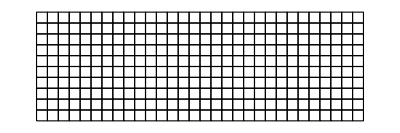

```mathematica
a=1.0;
reg1=Rectangle[{0,0},{30,10}];
(*reg2=Rectangle[{0,20},{5,40}];
reg3=Rectangle[{15,20},{20,40}];
reg4=Rectangle[{5,35},{15,40}];*)
(*Ω=RegionUnion[reg1,reg2,reg3,reg4];*)
mesh=ToElementMesh[reg1,"MaxCellMeasure"->1,"MeshOrder"->2,"MeshElementType"->QuadElement];
mesh["Wireframe"]
```

Defining boundary conditions

```mathematica
Subscript[Γ, Du]=DirichletCondition[u[x,y]==0.,(3.>x>0.&&y==0.)||(30.>x>27.&&y==0.)];
Subscript[Γ, Dv]=DirichletCondition[v[x,y]==0.,(3.>x>0.&&y==0.)||(30.>x>27.&&y==0.)];
Subscript[Γ, Nv]=NeumannValue[-1.,17.>x>13.&&y==0.];
```

Replacing the Young modulus and Poisson ratio in system of equations

```mathematica
op1=op/.{Y->3000.,ν->0.33};
```

Computations

```mathematica
{state}=NDSolve`ProcessEquations[{op1=={0.,Subscript[Γ, Nv]},Subscript[Γ, Du],Subscript[Γ, Dv]},{u,v},{x,y}∈mesh];
femdata=state["FiniteElementData"];
pded=femdata["PDECoefficientData"];
bcd=femdata["BoundaryConditionData"];
md=femdata["FEMMethodData"];
sd=state["SolutionData"][[1]];
vd=state["VariableData"];
discretePDE=DiscretizePDE[pded,md,sd];
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"];
discreteBCs=DiscretizeBoundaryConditions[bcd,md,sd];
ele=DiscretizePDE[pded,md,sd,"SaveFiniteElements"->True];
{stiffnessElements,nonzeroPos}=ele["StiffnessElements"];
```

Defining the densities and modified stiffness matrix

```mathematica
density=Table[ρ[i],{i,1,Length@stiffnessElements}];
modifiedElements=(density^2)*stiffnessElements;
Length@stiffnessElements
```

300

```mathematica
dof=md["DegreesOfFreedom"];
inci=Join@@md["Incidents"];
modifiedstiffness=AssembleMatrix[{inci,inci},modifiedElements,{dof,dof},"Sparse"->nonzeroPos];
displacement=Table[δ[i],{i,1,Length[stiffness]}];
coords=mesh["Coordinates"];
elems=mesh["MeshElements"];
DeployBoundaryConditions[{load,stiffness},discreteBCs];
DeployBoundaryConditions[{load,modifiedstiffness},discreteBCs];
loadF=mloadF=Flatten[load];
square=Join@@mesh["MeshElementMeasure"];
goalFunction=(*loadF.displacement*)displacement.modifiedstiffness.displacement;
massEquation=∑_(k=1)^Length[square] square⟦k⟧ density⟦k⟧≤(∑_(k=1)^Length[square] square⟦k⟧) 0.5;
densityEq=Thread[(0.≤#1≤1.&)[density]];
(*densityEq=(0.9≤#1≤1||0.0≤#1≤0.1)&/@density;*)
equation=Table[modifiedstiffness⟦i⟧.displacement==loadF⟦i⟧,{i,1,Length[displacement]}];
sysOfEq=Flatten[{goalFunction,massEquation,equation,densityEq}];
sysOfEq//Length;
variables=Flatten[{density,displacement}];
variables//Length;
initDis=Thread[{#,0}&[displacement]];
initDen=Thread[{#,0.5}&[density]];
initCond=Flatten[{initDen,initDis},1];
```

```mathematica
resultFMin=Quiet[FindMinimum[sysOfEq,initCond]];//AbsoluteTiming
```

{69.6149,Null}

```mathematica
minimizedDen=density/.resultFMin[[2]];
```

```mathematica
Evaluate[Table[ρ[i],{i,1,Length@stiffnessElements}]]=minimizedDen;
```

Solving for initial matrix and modified

```mathematica
Short[solution1=LinearSolve[stiffness,load]]
Short[solution2=LinearSolve[modifiedstiffness,load]]
```

{{-3.93735×10^-6},«1960»,{-0.000401221}}

{{-0.0000172536},«1960»,{-0.00106401}}

```mathematica
split=Span@@@Transpose[{Most[#+1],Rest[#]}&[md["IncidentOffsets"]]]
```

{1;;981,982;;1962}

```mathematica
ufun1=ElementMeshInterpolation[{mesh}, solution1[[split[[1]]]]];
vfun1=ElementMeshInterpolation[{mesh}, solution1[[split[[2]]]]];
ufun2=ElementMeshInterpolation[{mesh}, solution2[[split[[1]]]]];
vfun2=ElementMeshInterpolation[{mesh}, solution2[[split[[2]]]]];
```

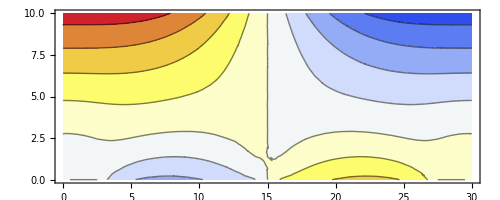
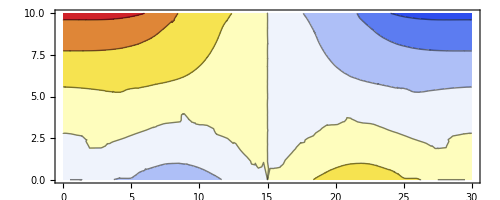

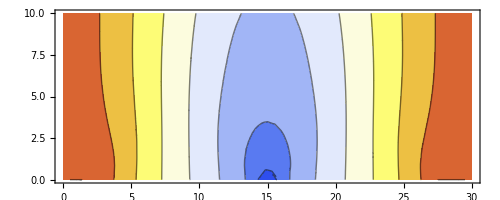
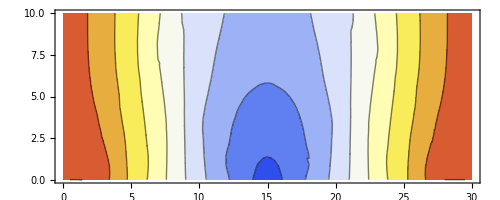

```mathematica
{ContourPlot[ufun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],ContourPlot[ufun2[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
{ContourPlot[vfun1[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic],
ContourPlot[vfun2[x,y],{x,y}∈mesh,ColorFunction->"Temperature",AspectRatio->Automatic]}
```

```mathematica
dmesh1=ElementMeshDeformation[mesh,{ufun1,vfun1}];
dmesh2=ElementMeshDeformation[mesh,{ufun2,vfun2}];
```

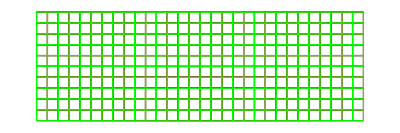

```mathematica
Show[{
mesh["Wireframe"],
dmesh1["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]],
dmesh2["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Green],FaceForm[]]]]
}]
```

#### Visualization of densities of elements for triangle elems

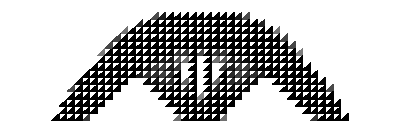

```mathematica
polys=Polygon[#]&/@(
Apply[{coords[[#1]],coords[[#2]],coords[[#3]]}&]/@elems[[1,1,1;;Length[square],1;;3]]);
maxden=Max[minimizedDen];
denpolys=Transpose[{minimizedDen/maxden,polys}];
filteredpolys=Select[denpolys,#[[1]]>0.0&];
opacityfiltered=Replace[#,{x_,y_}:>{Opacity[x],y}]&/@filteredpolys;
Graphics[opacityfiltered]
```

#### Visualization of densities of elements for quad elems

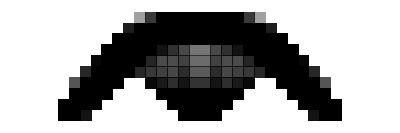

```mathematica
polys=Polygon[#]&/@(
Apply[{coords[[#1]],coords[[#2]],coords[[#3]],coords[[#4]]}&]/@elems[[1,1,1;;Length[square],1;;4]]);
maxden=Max[minimizedDen];
denpolys=Transpose[{minimizedDen/maxden,polys}];
filteredpolys=Select[denpolys,#[[1]]>0.0&];
opacityfiltered=Replace[#,{x_,y_}:>{Opacity[x],y}]&/@filteredpolys;
Graphics[opacityfiltered]
```

#### Density Interpolation

These values are values in elements. We’d need to get the values at the nodes. Here is a way to do it. “VertexElementConnectivity” shows which  vertex is connected to which elements 1 if there is a connection and 0 is there is no connection (see documentation of ElementMesh). We then use Mean to estimate a value at a node based on the connected elements.

```mathematica
denAtNodes=Mean/@DeleteCases[Inner[Times, mesh["VertexElementConnectivity"],minimizedDen,List],0.,2.];
```

```mathematica
denIF=ElementMeshInterpolation[{mesh},denAtNodes]
```

InterpolatingFunction[…]

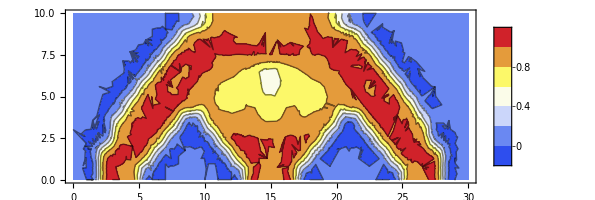

```mathematica
ContourPlot[denIF[x,y],{x,y}∈mesh,AspectRatio->Automatic,PlotLegends->Automatic]
```

#### Stress Analysis

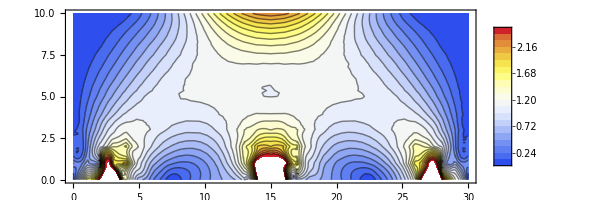

-Graphics-

```mathematica
fac=Y/(1-ν^2)*{{1,ν,0},{ν,1,0},{0,0,(1-ν)/2}}/.{Y->3000.,ν->0.33};;
mfun1=VonMisesStress[{ufun1,vfun1}, fac];
mfun2=VonMisesStress[{ufun2,vfun2}, fac];
ContourPlot[ mfun1[x,y],{x,0,30},{y,0,10},PlotLegends->Automatic,Contours->20]
ContourPlot[ mfun2[x,y],{x,0,30},{y,0,10},PlotLegends->Automatic,Contours->20]
```

#### ...

```mathematica
{c,d}={1,2}
```

```mathematica
density=density/.resultFMin[[2]];
```

```mathematica
ρ
```

```mathematica
Evaluate[Table[ρ[i],{i,1,10}]]=Range[10]
```

```mathematica
ρ[1]
```

#### Optimization in dynamic problems

```mathematica
Clear[u,v,x,y]
op={({{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}.v[x,y]{x,y}Inactive){x,y}Inactive+({{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}}.u[x,y]{x,y}Inactive){x,y}Inactive,({{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}}.u[x,y]{x,y}Inactive){x,y}Inactive+({{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}.v[x,y]{x,y}Inactive){x,y}Inactive};
```

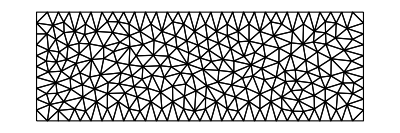

```mathematica
a=1.0;
reg1=Rectangle[{0,0},{30,10}];
(*reg2=Rectangle[{0,20},{5,40}];
reg3=Rectangle[{15,20},{20,40}];
reg4=Rectangle[{5,35},{15,40}];*)
(*Ω=RegionUnion[reg1,reg2,reg3,reg4];*)
mesh=ToElementMesh[reg1,"MaxCellMeasure"->1,"MeshOrder"->2,"MeshElementType"->TriangleElement];
mesh["Wireframe"]
```

```mathematica
Subscript[Γ, Du]=DirichletCondition[u[x,y]==0,x==0];
Subscript[Γ, Dv]=DirichletCondition[v[x,y]==0,x==0];
Subscript[Γ, Nv]=NeumannValue[-1,x==30&&3<y<7];
```

```mathematica
vd=NDSolve`VariableData[{"DependentVariables","Space"}->{{u,v},{x,y}}];
sd=NDSolve`SolutionData["Space"->ToNumericalRegion[mesh]];
methodData=InitializePDEMethodData[vd,sd]
```

FEMMethodData[<2050,{2,2},4>]

```mathematica
Length[mesh["Coordinates"]]*Length[NDSolve`SolutionDataComponent[vd,"DependentVariables"]]
methodData["DegreesOfFreedom"]
```

2050

2050

```mathematica
diffusionCoefficients="DiffusionCoefficients"->{{{{-Y/(1-ν^2),0},{0,-(Y (1-ν))/(2 (1-ν^2))}},{{0,-(Y ν)/(1-ν^2)},{-(Y (1-ν))/(2 (1-ν^2)),0}}},{{{0,-(Y (1-ν))/(2 (1-ν^2))},{-(Y ν)/(1-ν^2),0}},{{-(Y (1-ν))/(2 (1-ν^2)),0},{0,-Y/(1-ν^2)}}}}/.{Y->10^3,ν->33/100};
```

```mathematica
initCoeffs=InitializePDECoefficients[vd,sd,{diffusionCoefficients}];
```

```mathematica
initBCs=InitializeBoundaryConditions[vd,sd,{{Subscript[Γ, Du]},{Subscript[Γ, Dv],Subscript[Γ, Nv]}}];
```

```mathematica
discretePDE=DiscretizePDE[initCoeffs,methodData,sd];
```

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

```mathematica
split=Span@@@Transpose[{Most[#+1],Rest[#]}&[methodData["IncidentOffsets"]]];
```

```mathematica
discreteBCs=DiscretizeBoundaryConditions[initBCs,methodData,sd];
```

```mathematica
massCoefficients="MassCoefficients"->{{1,0},{0,1}}
```

```mathematica
"MassCoefficients"->{{1,0},{0,1}}
```

MassCoefficients→{{1,0},{0,1}}

```mathematica
initCoeffs=InitializePDECoefficients[vd,sd,{diffusionCoefficients,massCoefficients}]
```

PDECoefficientData[<2,2>]

```mathematica
discretePDE=DiscretizePDE[initCoeffs,methodData,sd]
```

DiscretizedPDEData[<2050>]

```mathematica
{load,stiffness,damping,mass}=discretePDE["SystemMatrices"]
```

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

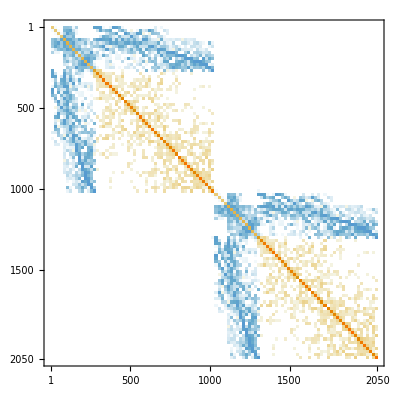

```mathematica
MatrixPlot[mass]
```

```mathematica
rayleighDamping=0.1*mass+0.04*stiffness;
```

```mathematica
DeployBoundaryConditions[{load,stiffness,rayleighDamping,mass},discreteBCs]
```

DeployedBoundaryConditionData[<Insert>]

```mathematica
dof=methodData["DegreesOfFreedom"];
init=dinit=ConstantArray[0,{dof,1}];
```

```mathematica
sparsity=ArrayFlatten[{{mass["PatternArray"],mass["PatternArray"]},{rayleighDamping["PatternArray"],rayleighDamping["PatternArray"]}}]
```

SparseArray[<132132>, {4100, 4100}, Pattern]

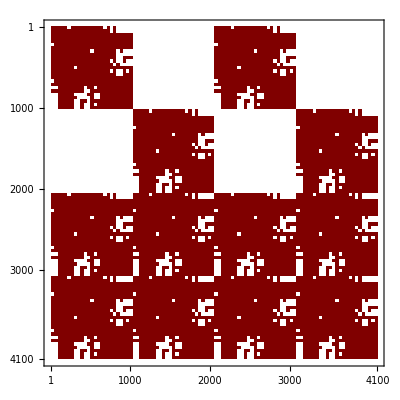

```mathematica
MatrixPlot[sparsity]
```

```mathematica
Dynamic["time: "<>ToString[CForm[currentTime]]]
AbsoluteTiming[
tfun=NDSolveValue[{
mass.u''[ t]+rayleighDamping.u'[ t]+stiffness.u[ t]==load*Sin[t*0.1]*5
,u[ 0]==init,u'[ 0]==dinit},u,{t,0,450}
,Method->{"EquationSimplification"->"Residual"}
,Jacobian->{Automatic,Sparse->sparsity}
,EvaluationMonitor:>(currentTime=t;)
]]
```

{26.6825,InterpolatingFunction[{{0., 450.}}, <>]}

```mathematica
graphics=Function[t,
dmesh=ElementMeshDeformation[mesh,Part[tfun[t],#]&/@split];
Show[{
mesh["Wireframe"["MeshElement"->"BoundaryElements"]],
dmesh["Wireframe"["ElementMeshDirective"->Directive[EdgeForm[Red],FaceForm[]]]]
},PlotRange->{{-1,31},{-1,11}}]]/@Range[0,450,1];
```

```mathematica
ListAnimate[graphics,SaveDefinitions->True]
```

```mathematica
energyF[t_]:=Flatten[tfun[t]].stiffness.Flatten[tfun[t]]
```

```mathematica
stiffness//Length
```

2050

```mathematica
tfun[1]//Length
```

2050

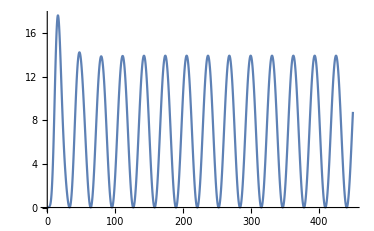

```mathematica
Plot[energyF[t],{t,0,450}]
```

#### Results

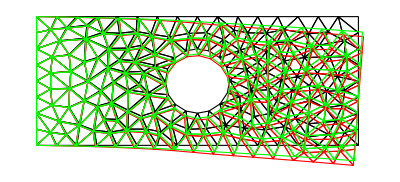

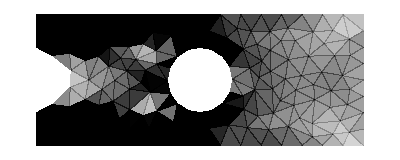

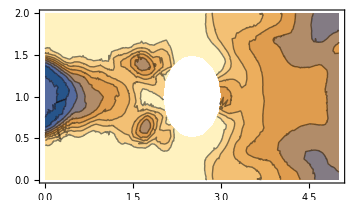

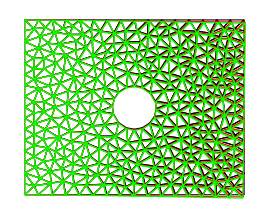

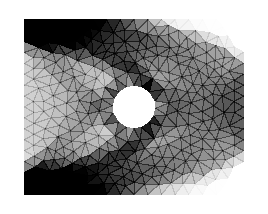

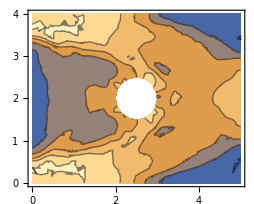

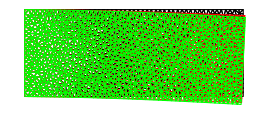

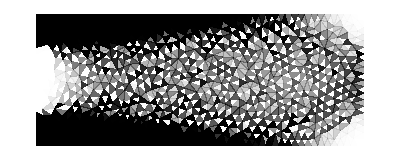

```mathematica
-Graphics--Graphics--Graphics-
```